Run this first

### definition of MATHUSLA geometry and functions for computing event yield

#### playing around with boxes and ray intersections

```mathematica
θfromη[η_]:=2 ArcCot[ⅇ^η]
ηfromθ[θ_]:=-Log[Tan[θ/2]];
```

```mathematica
planesegmentParametricDefinition[currentplanesegment_]:=Module[{twocoordposns,basepoint,corner1,corner2},
twocoordposns=Position[currentplanesegment,x_/;Length[x]==2]//Flatten;
basepoint={If[Length[currentplanesegment[[1]]]==2,currentplanesegment[[1]][[1]],currentplanesegment[[1]]],
If[Length[currentplanesegment[[2]]]==2,currentplanesegment[[2]][[1]],currentplanesegment[[2]]],
If[Length[currentplanesegment[[3]]]==2,currentplanesegment[[3]][[1]],currentplanesegment[[3]]]};
corner1=basepoint;
corner1[[twocoordposns[[1]]]]=currentplanesegment[[twocoordposns[[1]]]][[2]];
corner2=basepoint;
corner2[[twocoordposns[[2]]]]=currentplanesegment[[twocoordposns[[2]]]][[2]];
basepoint + t (corner1-basepoint) + w (corner2 - basepoint)
]

planesegmentsfromboxdefinition[boxdefinition_]:={
{boxdefinition[[1]],boxdefinition[[2]],boxdefinition[[3]][[1]]}
,
{boxdefinition[[1]],boxdefinition[[2]],boxdefinition[[3]][[2]]}
,
{boxdefinition[[1]],boxdefinition[[2]][[1]],boxdefinition[[3]]}
,
{boxdefinition[[1]],boxdefinition[[2]][[2]],boxdefinition[[3]]}
,
{boxdefinition[[1]][[1]],boxdefinition[[2]],boxdefinition[[3]]}
,
{boxdefinition[[1]][[2]],boxdefinition[[2]],boxdefinition[[3]]}
}
```

## Tests

```mathematica
boxdefinition=boxdefinitionMATHUSLA={{-10,10},{-100,100},{100,300}}
```

{{-10,10},{-100,100},{100,300}}

```mathematica
planesegmentsfromboxdefinition[boxdefinition]
```

{{{-10,10},{-100,100},100},{{-10,10},{-100,100},300},{{-10,10},-100,{100,300}},{{-10,10},100,{100,300}},{-10,{-100,100},{100,300}},{10,{-100,100},{100,300}}}

```mathematica
planesegmentsfromboxdefinition[boxdefinition][[3]]
```

{{-10,10},-100,{100,300}}

```mathematica
twocoordposns=Position[planesegmentsfromboxdefinition[boxdefinition][[3]],x_/;Length[x]==2]//Flatten
```

{1,3}

```mathematica
planesegmentParametricDefinition[planesegmentsfromboxdefinition[boxdefinition][[6]]]
```

{10,-100+200 t,100+200 w}

```mathematica
{lineθ,lineϕ}={0,0};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};
```

```mathematica
(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition])
```

{{-10+20 t,-100+200 w,100},{-10+20 t,-100+200 w,300},{-10+20 t,-100,100+200 w},{-10+20 t,100,100+200 w},{-10,-100+200 t,100+200 w},{10,-100+200 t,100+200 w}}

```mathematica
Solve[Evaluate[currentline==#],{s,t,w}]&/@(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition])
```

{{{s→100,t→1/2,w→1/2}},{{s→300,t→1/2,w→1/2}},{},{},{},{}}

```mathematica
Flatten[%,1]
```

{{s→100,t→1/2,w→1/2},{s→300,t→1/2,w→1/2}}

```mathematica
Select[%,(0≤ (t/.#)≤ 1) && (0≤ (w/.#)≤ 1 ) && (s/.#)≥0&]
```

{{s→100,t→1/2,w→1/2},{s→300,t→1/2,w→1/2}}

```mathematica
intersectionsolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,t,w}]&/@(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]),1]
,(0≤ (t/.#)≤ 1) && (0≤ (w/.#)≤ 1 ) && (s/.#)≥0&]
```

{{s→160.207,t→0.627671,w→0.112667},{s→192.249,t→0.653205,w→0.235201}}

```mathematica
intersectionpoints=If[Length[intersectionsolutions]>0,
Sort[currentline/.intersectionsolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
]
```

{{100.,25.5342,122.533},{120.,30.641,147.04}}

```mathematica
{√(intersectionpoints[[1]].intersectionpoints[[1]]),√(intersectionpoints[[2]].intersectionpoints[[2]])}
```

{160.207,192.249}

```mathematica
L2mL1asfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionsolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,t,w}]&/@(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]),1]
,(0≤ (t/.#)≤ 1) && (0≤ (w/.#)≤ 1 )&& (s/.#)≥0&];

intersectionpoints=If[Length[intersectionsolutions]>0,
Sort[currentline/.intersectionsolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
];

√(intersectionpoints[[2]].intersectionpoints[[2]])-√(intersectionpoints[[1]].intersectionpoints[[1]])
}
,{cosθ,1,-1,-0.1},{ϕ,-π,π,2π/20}],1]
```

{{1.,-π,0},{1.,-(9 π)/10,0},{1.,-(4 π)/5,0},{1.,-(7 π)/10,0},{1.,-(3 π)/5,0},{1.,-π/2,0},{1.,-(2 π)/5,0},{1.,-(3 π)/10,0},{1.,-π/5,0},{1.,-π/10,0},{1.,0,0},{1.,π/10,0},{1.,π/5,0},{1.,(3 π)/10,0},{1.,(2 π)/5,0},{1.,π/2,0},{1.,(3 π)/5,0},{1.,(7 π)/10,0},{1.,(4 π)/5,0},{1.,(9 π)/10,0},{1.,π,0},{0.9,-π,0},{0.9,-(9 π)/10,0},{0.9,-(4 π)/5,0},{0.9,-(7 π)/10,0},{0.9,-(3 π)/5,0},{0.9,-π/2,0},{0.9,-(2 π)/5,0},{0.9,-(3 π)/10,0},{0.9,-π/5,49.7599},{0.9,-π/10,48.2444},{0.9,0,45.8831},{0.9,π/10,48.2444},{0.9,π/5,49.7599},{0.9,(3 π)/10,0},{0.9,(2 π)/5,0},{0.9,π/2,0},{0.9,(3 π)/5,0},{0.9,(7 π)/10,0},{0.9,(4 π)/5,0},{0.9,(9 π)/10,0},{0.9,π,0},{0.8,-π,0},{0.8,-(9 π)/10,0},{0.8,-(4 π)/5,0},{0.8,-(7 π)/10,0},{0.8,-(3 π)/5,0},{0.8,-π/2,0},{0.8,-(2 π)/5,0},{0.8,-(3 π)/10,0},{0.8,-π/5,41.2023},{0.8,-π/10,35.0487},{0.8,0,33.3333},{0.8,π/10,35.0487},{0.8,π/5,41.2023},{0.8,(3 π)/10,0},{0.8,(2 π)/5,0},{0.8,π/2,0},{0.8,(3 π)/5,0},{0.8,(7 π)/10,0},{0.8,(4 π)/5,0},{0.8,(9 π)/10,0},{0.8,π,0},{0.7,-π,0},{0.7,-(9 π)/10,0},{0.7,-(4 π)/5,0},{0.7,-(7 π)/10,0},{0.7,-(3 π)/5,0},{0.7,-π/2,0},{0.7,-(2 π)/5,0},{0.7,-(3 π)/10,0},{0.7,-π/5,34.6168},{0.7,-π/10,29.4468},{0.7,0,25.1765},{0.7,π/10,29.4468},{0.7,π/5,34.6168},{0.7,(3 π)/10,0},{0.7,(2 π)/5,0},{0.7,π/2,0},{0.7,(3 π)/5,0},{0.7,(7 π)/10,0},{0.7,(4 π)/5,0},{0.7,(9 π)/10,0},{0.7,π,0},{0.6,-π,0},{0.6,-(9 π)/10,0},{0.6,-(4 π)/5,0},{0.6,-(7 π)/10,0},{0.6,-(3 π)/5,0},{0.6,-π/2,0},{0.6,-(2 π)/5,0},{0.6,-(3 π)/10,0},{0.6,-π/5,18.7435},{0.6,-π/10,0},{0.6,0,0},{0.6,π/10,0},{0.6,π/5,18.7435},{0.6,(3 π)/10,0},{0.6,(2 π)/5,0},{0.6,π/2,0},{0.6,(3 π)/5,0},{0.6,(7 π)/10,0},{0.6,(4 π)/5,0},{0.6,(9 π)/10,0},{0.6,π,0},{0.5,-π,0},{0.5,-(9 π)/10,0},{0.5,-(4 π)/5,0},{0.5,-(7 π)/10,0},{0.5,-(3 π)/5,0},{0.5,-π/2,0},{0.5,-(2 π)/5,0},{0.5,-(3 π)/10,0},{0.5,-π/5,0},{0.5,-π/10,0},{0.5,0,0},{0.5,π/10,0},{0.5,π/5,0},{0.5,(3 π)/10,0},{0.5,(2 π)/5,0},{0.5,π/2,0},{0.5,(3 π)/5,0},{0.5,(7 π)/10,0},{0.5,(4 π)/5,0},{0.5,(9 π)/10,0},{0.5,π,0},{0.4,-π,0},{0.4,-(9 π)/10,0},{0.4,-(4 π)/5,0},{0.4,-(7 π)/10,0},{0.4,-(3 π)/5,0},{0.4,-π/2,0},{0.4,-(2 π)/5,0},{0.4,-(3 π)/10,0},{0.4,-π/5,0},{0.4,-π/10,0},{0.4,0,0},{0.4,π/10,0},{0.4,π/5,0},{0.4,(3 π)/10,0},{0.4,(2 π)/5,0},{0.4,π/2,0},{0.4,(3 π)/5,0},{0.4,(7 π)/10,0},{0.4,(4 π)/5,0},{0.4,(9 π)/10,0},{0.4,π,0},{0.3,-π,0},{0.3,-(9 π)/10,0},{0.3,-(4 π)/5,0},{0.3,-(7 π)/10,0},{0.3,-(3 π)/5,0},{0.3,-π/2,0},{0.3,-(2 π)/5,0},{0.3,-(3 π)/10,0},{0.3,-π/5,0},{0.3,-π/10,0},{0.3,0,0},{0.3,π/10,0},{0.3,π/5,0},{0.3,(3 π)/10,0},{0.3,(2 π)/5,0},{0.3,π/2,0},{0.3,(3 π)/5,0},{0.3,(7 π)/10,0},{0.3,(4 π)/5,0},{0.3,(9 π)/10,0},{0.3,π,0},{0.2,-π,0},{0.2,-(9 π)/10,0},{0.2,-(4 π)/5,0},{0.2,-(7 π)/10,0},{0.2,-(3 π)/5,0},{0.2,-π/2,0},{0.2,-(2 π)/5,0},{0.2,-(3 π)/10,0},{0.2,-π/5,0},{0.2,-π/10,0},{0.2,0,0},{0.2,π/10,0},{0.2,π/5,0},{0.2,(3 π)/10,0},{0.2,(2 π)/5,0},{0.2,π/2,0},{0.2,(3 π)/5,0},{0.2,(7 π)/10,0},{0.2,(4 π)/5,0},{0.2,(9 π)/10,0},{0.2,π,0},{0.1,-π,0},{0.1,-(9 π)/10,0},{0.1,-(4 π)/5,0},{0.1,-(7 π)/10,0},{0.1,-(3 π)/5,0},{0.1,-π/2,0},{0.1,-(2 π)/5,0},{0.1,-(3 π)/10,0},{0.1,-π/5,0},{0.1,-π/10,0},{0.1,0,0},{0.1,π/10,0},{0.1,π/5,0},{0.1,(3 π)/10,0},{0.1,(2 π)/5,0},{0.1,π/2,0},{0.1,(3 π)/5,0},{0.1,(7 π)/10,0},{0.1,(4 π)/5,0},{0.1,(9 π)/10,0},{0.1,π,0},{0.,-π,0},{0.,-(9 π)/10,0},{0.,-(4 π)/5,0},{0.,-(7 π)/10,0},{0.,-(3 π)/5,0},{0.,-π/2,0},{0.,-(2 π)/5,0},{0.,-(3 π)/10,0},{0.,-π/5,0},{0.,-π/10,0},{0.,0,0},{0.,π/10,0},{0.,π/5,0},{0.,(3 π)/10,0},{0.,(2 π)/5,0},{0.,π/2,0},{0.,(3 π)/5,0},{0.,(7 π)/10,0},{0.,(4 π)/5,0},{0.,(9 π)/10,0},{0.,π,0},{-0.1,-π,0},{-0.1,-(9 π)/10,0},{-0.1,-(4 π)/5,0},{-0.1,-(7 π)/10,0},{-0.1,-(3 π)/5,0},{-0.1,-π/2,0},{-0.1,-(2 π)/5,0},{-0.1,-(3 π)/10,0},{-0.1,-π/5,0},{-0.1,-π/10,0},{-0.1,0,0},{-0.1,π/10,0},{-0.1,π/5,0},{-0.1,(3 π)/10,0},{-0.1,(2 π)/5,0},{-0.1,π/2,0},{-0.1,(3 π)/5,0},{-0.1,(7 π)/10,0},{-0.1,(4 π)/5,0},{-0.1,(9 π)/10,0},{-0.1,π,0},{-0.2,-π,0},{-0.2,-(9 π)/10,0},{-0.2,-(4 π)/5,0},{-0.2,-(7 π)/10,0},{-0.2,-(3 π)/5,0},{-0.2,-π/2,0},{-0.2,-(2 π)/5,0},{-0.2,-(3 π)/10,0},{-0.2,-π/5,0},{-0.2,-π/10,0},{-0.2,0,0},{-0.2,π/10,0},{-0.2,π/5,0},{-0.2,(3 π)/10,0},{-0.2,(2 π)/5,0},{-0.2,π/2,0},{-0.2,(3 π)/5,0},{-0.2,(7 π)/10,0},{-0.2,(4 π)/5,0},{-0.2,(9 π)/10,0},{-0.2,π,0},{-0.3,-π,0},{-0.3,-(9 π)/10,0},{-0.3,-(4 π)/5,0},{-0.3,-(7 π)/10,0},{-0.3,-(3 π)/5,0},{-0.3,-π/2,0},{-0.3,-(2 π)/5,0},{-0.3,-(3 π)/10,0},{-0.3,-π/5,0},{-0.3,-π/10,0},{-0.3,0,0},{-0.3,π/10,0},{-0.3,π/5,0},{-0.3,(3 π)/10,0},{-0.3,(2 π)/5,0},{-0.3,π/2,0},{-0.3,(3 π)/5,0},{-0.3,(7 π)/10,0},{-0.3,(4 π)/5,0},{-0.3,(9 π)/10,0},{-0.3,π,0},{-0.4,-π,0},{-0.4,-(9 π)/10,0},{-0.4,-(4 π)/5,0},{-0.4,-(7 π)/10,0},{-0.4,-(3 π)/5,0},{-0.4,-π/2,0},{-0.4,-(2 π)/5,0},{-0.4,-(3 π)/10,0},{-0.4,-π/5,0},{-0.4,-π/10,0},{-0.4,0,0},{-0.4,π/10,0},{-0.4,π/5,0},{-0.4,(3 π)/10,0},{-0.4,(2 π)/5,0},{-0.4,π/2,0},{-0.4,(3 π)/5,0},{-0.4,(7 π)/10,0},{-0.4,(4 π)/5,0},{-0.4,(9 π)/10,0},{-0.4,π,0},{-0.5,-π,0},{-0.5,-(9 π)/10,0},{-0.5,-(4 π)/5,0},{-0.5,-(7 π)/10,0},{-0.5,-(3 π)/5,0},{-0.5,-π/2,0},{-0.5,-(2 π)/5,0},{-0.5,-(3 π)/10,0},{-0.5,-π/5,0},{-0.5,-π/10,0},{-0.5,0,0},{-0.5,π/10,0},{-0.5,π/5,0},{-0.5,(3 π)/10,0},{-0.5,(2 π)/5,0},{-0.5,π/2,0},{-0.5,(3 π)/5,0},{-0.5,(7 π)/10,0},{-0.5,(4 π)/5,0},{-0.5,(9 π)/10,0},{-0.5,π,0},{-0.6,-π,0},{-0.6,-(9 π)/10,0},{-0.6,-(4 π)/5,0},{-0.6,-(7 π)/10,0},{-0.6,-(3 π)/5,0},{-0.6,-π/2,0},{-0.6,-(2 π)/5,0},{-0.6,-(3 π)/10,0},{-0.6,-π/5,0},{-0.6,-π/10,0},{-0.6,0,0},{-0.6,π/10,0},{-0.6,π/5,0},{-0.6,(3 π)/10,0},{-0.6,(2 π)/5,0},{-0.6,π/2,0},{-0.6,(3 π)/5,0},{-0.6,(7 π)/10,0},{-0.6,(4 π)/5,0},{-0.6,(9 π)/10,0},{-0.6,π,0},{-0.7,-π,0},{-0.7,-(9 π)/10,0},{-0.7,-(4 π)/5,0},{-0.7,-(7 π)/10,0},{-0.7,-(3 π)/5,0},{-0.7,-π/2,0},{-0.7,-(2 π)/5,0},{-0.7,-(3 π)/10,0},{-0.7,-π/5,0},{-0.7,-π/10,0},{-0.7,0,0},{-0.7,π/10,0},{-0.7,π/5,0},{-0.7,(3 π)/10,0},{-0.7,(2 π)/5,0},{-0.7,π/2,0},{-0.7,(3 π)/5,0},{-0.7,(7 π)/10,0},{-0.7,(4 π)/5,0},{-0.7,(9 π)/10,0},{-0.7,π,0},{-0.8,-π,0},{-0.8,-(9 π)/10,0},{-0.8,-(4 π)/5,0},{-0.8,-(7 π)/10,0},{-0.8,-(3 π)/5,0},{-0.8,-π/2,0},{-0.8,-(2 π)/5,0},{-0.8,-(3 π)/10,0},{-0.8,-π/5,0},{-0.8,-π/10,0},{-0.8,0,0},{-0.8,π/10,0},{-0.8,π/5,0},{-0.8,(3 π)/10,0},{-0.8,(2 π)/5,0},{-0.8,π/2,0},{-0.8,(3 π)/5,0},{-0.8,(7 π)/10,0},{-0.8,(4 π)/5,0},{-0.8,(9 π)/10,0},{-0.8,π,0},{-0.9,-π,0},{-0.9,-(9 π)/10,0},{-0.9,-(4 π)/5,0},{-0.9,-(7 π)/10,0},{-0.9,-(3 π)/5,0},{-0.9,-π/2,0},{-0.9,-(2 π)/5,0},{-0.9,-(3 π)/10,0},{-0.9,-π/5,0},{-0.9,-π/10,0},{-0.9,0,0},{-0.9,π/10,0},{-0.9,π/5,0},{-0.9,(3 π)/10,0},{-0.9,(2 π)/5,0},{-0.9,π/2,0},{-0.9,(3 π)/5,0},{-0.9,(7 π)/10,0},{-0.9,(4 π)/5,0},{-0.9,(9 π)/10,0},{-0.9,π,0},{-1.,-π,0},{-1.,-(9 π)/10,0},{-1.,-(4 π)/5,0},{-1.,-(7 π)/10,0},{-1.,-(3 π)/5,0},{-1.,-π/2,0},{-1.,-(2 π)/5,0},{-1.,-(3 π)/10,0},{-1.,-π/5,0},{-1.,-π/10,0},{-1.,0,0},{-1.,π/10,0},{-1.,π/5,0},{-1.,(3 π)/10,0},{-1.,(2 π)/5,0},{-1.,π/2,0},{-1.,(3 π)/5,0},{-1.,(7 π)/10,0},{-1.,(4 π)/5,0},{-1.,(9 π)/10,0},{-1.,π,0}}

```mathematica
Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[1]]
```

{0.9,0.9,0.9,0.9,0.9,0.8,0.8,0.8,0.8,0.8,0.7,0.7,0.7,0.7,0.7,0.6,0.6}

```mathematica
(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[1]]//Max[#]-Min[#]&)
```

0.3

## Back to the regular program

{{100,120},{-100,100},{100,300}}

{{s→208.583,t→0.5,w→0.415244},{s→250.3,t→0.5,w→0.598293}}

{{100.,0.,183.049},{120.,0.,219.659}}

{208.583,250.3}

-Graphics3D-

estimate geometric coverage

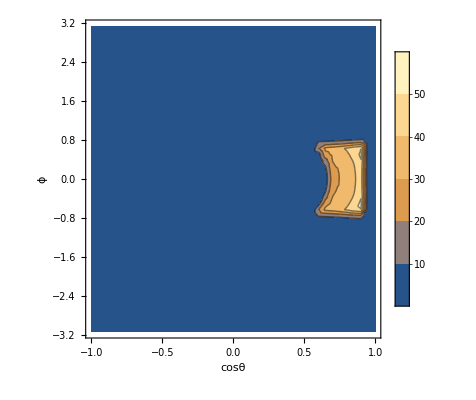

fraction of solid angle covered:

0.036

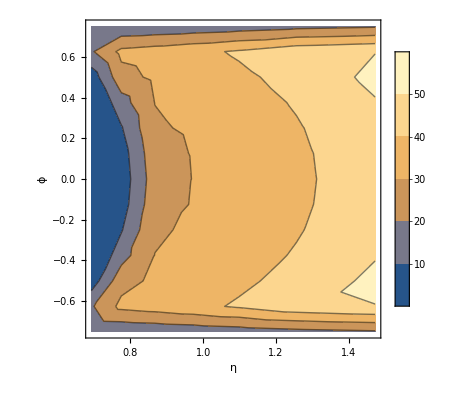

0.672102

```mathematica
boxdefinition=boxdefinitionMATHUSLA={{100,120},{-100,100},{100,300}}


{lineθ,lineϕ}={0.5,0};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionsolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,t,w}]&/@(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]),1]
,(0≤ (t/.#)≤ 1) && (0≤ (w/.#)≤ 1 ) && (s/.#)≥0&]

intersectionpoints=If[Length[intersectionsolutions]>0,
Sort[currentline/.intersectionsolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
]

{√(intersectionpoints[[1]].intersectionpoints[[1]]),√(intersectionpoints[[2]].intersectionpoints[[2]])}

Show[
ParametricPlot3D[{
Evaluate[planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]]
},{t,0,1},{w,0,1},
PlotRange->{{-1,1},{-1,1},{-1,1}}300,BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[currentline,{s,0,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"}]
,
ListPointPlot3D[intersectionpoints,PlotStyle->{Red,PointSize[0.02]}]
]



"estimate geometric coverage"
L2mL1asfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionsolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,t,w}]&/@(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]),1]
,(0≤ (t/.#)≤ 1) && (0≤ (w/.#)≤ 1 )&& (s/.#)≥0&];

intersectionpoints=If[Length[intersectionsolutions]>0,
Sort[currentline/.intersectionsolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
];

√(intersectionpoints[[2]].intersectionpoints[[2]])-√(intersectionpoints[[1]].intersectionpoints[[1]])
}
,{cosθ,1,-1,-0.05},{ϕ,-π,π,2π/50}],1];

ListContourPlot[L2mL1asfncosθϕ,PlotLegends->Automatic, FrameLabel->{"cosθ","ϕ"}]


"fraction of solid angle covered:"
1/(4π)(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[1]]//Max[#]-Min[#]&)(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[2]]//Max[#]-Min[#]&)


ListContourPlot[{ArcCos[#[[1]]]//ηfromθ,#[[2]],#[[3]]}&/@Select[L2mL1asfncosθϕ,#[[3]]>0&],PlotLegends->Automatic, FrameLabel->{"η","ϕ"}]


(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[1]]//ηfromθ[Min[#]]-ηfromθ[Max[#]]&)(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[2]]//Max[#]-Min[#]&)
```

```mathematica
cosθϕrangeMATHUSLA=Findcosθϕrange[boxdefinitionMATHUSLA];
```

#### defining detector L1L2 fns and functions for obtaining final event yield

```mathematica
DecayProb[L1_?NumericQ,L2_?NumericQ,bλ_?NumericQ]=ⅇ^(-L1/bλ)-ⅇ^(-L2/bλ);
```

```mathematica
BoxDetectorL1L2m[θ_,ϕ_,boxdefinition_]:=Module[{cosθ},
cosθ=Cos[θ];
{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionsolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,t,w}]&/@(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]),1]
,(0≤ (t/.#)≤ 1) && (0≤ (w/.#)≤ 1 )&& (s/.#)≥0&];

intersectionpoints=If[Length[intersectionsolutions]>0,
Sort[currentline/.intersectionsolutions,#1.#1<#2.#2&]
,
{1/(√3){ⅈ,ⅈ,ⅈ},1/(√3){ⅈ,ⅈ,ⅈ}}
];

{√(intersectionpoints[[1]].intersectionpoints[[1]]),√(intersectionpoints[[2]].intersectionpoints[[2]])}
];


ClearAll[Findcosθϕrange]

Findcosθϕrange[boxdefinition_,cosθstep_:2/20,ϕstep_:2π/20]:=Module[{},

L2mL1asfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionsolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,t,w}]&/@(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]),1]
,(0≤ (t/.#)≤ 1) && (0≤ (w/.#)≤ 1 )&& (s/.#)≥0&];

intersectionpoints=If[Length[intersectionsolutions]>0,
Sort[currentline/.intersectionsolutions,#1.#1<#2.#2&]
,
{1/(√3){ⅈ,ⅈ,ⅈ},1/(√3){ⅈ,ⅈ,ⅈ}}
];

√(intersectionpoints[[2]].intersectionpoints[[2]])-√(intersectionpoints[[1]].intersectionpoints[[1]])
}
,{cosθ,1,-1,-cosθstep},{ϕ,-π,π,ϕstep}],1];


{(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[1]]//{Min[#]-cosθstep,Max[#]+cosθstep}&)
,(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[2]]//{Min[#]-ϕstep,Max[#]+ϕstep}&)
}


];
```

```mathematica
ComputeDecayEfficiencyBoxDetector[θblist_, currentcτmeters_, boxdefinition_,currentcosθϕrange_]:=Module[{θblistflat},
θblistflat=Flatten[θblist,1];
(*we choose ϕ randomly to lie within the range covered by the box detector, and weigh accordingly*)
(*(this would obviously not be ok if we wanted to detect two particles per event, since the ϕ correlations have been thrown out, but doesn't matter for us)*)
(currentcosθϕrange[[2]][[2]]-currentcosθϕrange[[2]][[1]])/(2π)( Sum[
X1=θblistflat[[i]];
PX1inBox=(DecayProb[#1⟦1⟧,#1⟦2⟧,currentcτmeters X1⟦2⟧]&)[BoxDetectorL1L2m[X1⟦1⟧,RandomReal[currentcosθϕrange[[2]]],boxdefinition]];
{PX1inBox,PX1inBox^2}
,{i,1,Length[θblistflat]}]
//{#[[1]],√(#[[2]])}&
)/Length[θblist]//Re
]
```

## Test round 2

```mathematica
(Sqrt[{#1⟦1⟧^2,#1⟦2⟧^2}]&)[{7,9}]
```

{7,9}

```mathematica
Sum[{i,i^2},{i,1,10}]//{#[[1]],√(#[[2]])}&
```

{55,√385}

## Cylinder Geometry

#### Setting up cylinder parametric definitions

```mathematica
planeSegmentsFromCylinder[cylinderDef_]:={
{cylinderDef[[1]]+r*Sin[α],cylinderDef[[2]]+r*Cos[α],cylinderDef[[3]]}
,
{cylinderDef[[1]]+r*Sin[α],cylinderDef[[2]]+r*Cos[α],cylinderDef[[3]]+cylinderDef[[4]]}
,
{cylinderDef[[1]] +cylinderDef[[5]]*Sin[α],cylinderDef[[2]]+cylinderDef[[5]]*Cos[α],cylinderDef[[3]]+l}
}
```

## Tests

```mathematica
cylinderDef ={0,0, 10,10,5} (*In the form x,y,z (of the first cap centre), length, and radius. All in m. x is up, y is to the right, and z is down the beampipe*)
```

{0,0,10,10,5}

```mathematica
planeSegmentsFromCylinder[cylinderDef]
```

{{r Sin[α],r Cos[α],10},{r Sin[α],r Cos[α],20},{5 Sin[α],5 Cos[α],10+l}}

```mathematica
{lineθ,lineϕ}={0.00,0.001};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]}
```

{0.,0.,1. s}

```mathematica
Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromCylinder[cylinderDef])/.C[1]-> 0
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{{s→10.,r→0.}},{{s→20.,r→0.}},{}}

```mathematica
Flatten[%,1]
```

{{s→10.,r→0.},{s→20.,r→0.}}

```mathematica
Select[%,((0≤ (r/.#)≤ cylinderDef[[5]]) && (s/.#)≥0  (*&& (α/.#)≥-3.1415 *))||((0≤ (l/.#)≤ cylinderDef[[4]]) && (s/.#)≥0 )&]
```

{{s→10.,r→0.},{s→20.,r→0.}}

```mathematica
intersectionCylinderSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromCylinder[cylinderDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤ cylinderDef[[5]]) && (s/.#)≥0 (*&& (α/.#)≥-3.1415*))||((0≤ (l/.#)≤ cylinderDef[[4]]) && (s/.#)≥0 )&]//Quiet
```

{{s→10.,r→0.},{s→20.,r→0.}}

```mathematica
cylinderIntersectionPoints=If[Length[intersectionCylinderSolutions]>0,
Sort[currentline/.intersectionCylinderSolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
]
```

{{0.,0.,10.},{0.,0.,20.}}

```mathematica
{√(cylinderIntersectionPoints[[1]].cylinderIntersectionPoints[[1]]),√(cylinderIntersectionPoints[[2]].cylinderIntersectionPoints[[2]])}
√(cylinderIntersectionPoints[[2]].cylinderIntersectionPoints[[2]])-√(cylinderIntersectionPoints[[1]].cylinderIntersectionPoints[[1]])
```

{10.,20.}

10.

```mathematica
L2mL1Cylasfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionCylinderSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromCylinder[cylinderDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤ cylinderDef[[5]]) && (s/.#)≥0 )||((0≤ (l/.#)≤ cylinderDef[[4]]) && (s/.#)≥0 )&]//Quiet;

cylinderIntersectionPoints=If[Length[intersectionCylinderSolutions]>0,
Sort[currentline/.intersectionCylinderSolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
];

√(cylinderIntersectionPoints[[2]].cylinderIntersectionPoints[[2]])-√(cylinderIntersectionPoints[[1]].cylinderIntersectionPoints[[1]])
}
,{cosθ,1,-1,-0.1},{ϕ,-π,π,π/10}],1]
```

{{1.,-π,10.},{1.,-(9 π)/10,10.},{1.,-(4 π)/5,10.},{1.,-(7 π)/10,10.},{1.,-(3 π)/5,10.},{1.,-π/2,10.},{1.,-(2 π)/5,10.},{1.,-(3 π)/10,10.},{1.,-π/5,10.},{1.,-π/10,10.},{1.,0,10.},{1.,π/10,10.},{1.,π/5,10.},{1.,(3 π)/10,10.},{1.,(2 π)/5,10.},{1.,π/2,10.},{1.,(3 π)/5,10.},{1.,(7 π)/10,10.},{1.,(4 π)/5,10.},{1.,(9 π)/10,10.},{1.,π,10.},{0.9,-π,0.359676},{0.9,-(9 π)/10,0.359676},{0.9,-(4 π)/5,0.359676},{0.9,-(7 π)/10,0.359676},{0.9,-(3 π)/5,0.359676},{0.9,-π/2,0.},{0.9,-(2 π)/5,0.359676},{0.9,-(3 π)/10,0.359676},{0.9,-π/5,0.359676},{0.9,-π/10,0.359676},{0.9,0,0.359676},{0.9,π/10,0.359676},{0.9,π/5,0.359676},{0.9,(3 π)/10,0.359676},{0.9,(2 π)/5,0.359676},{0.9,π/2,0.359676},{0.9,(3 π)/5,0.359676},{0.9,(7 π)/10,0.359676},{0.9,(4 π)/5,0.359676},{0.9,(9 π)/10,0.359676},{0.9,π,0.359676},{0.8,-π,0},{0.8,-(9 π)/10,0},{0.8,-(4 π)/5,0},{0.8,-(7 π)/10,0},{0.8,-(3 π)/5,0},{0.8,-π/2,0},{0.8,-(2 π)/5,0},{0.8,-(3 π)/10,0},{0.8,-π/5,0},{0.8,-π/10,0},{0.8,0,0},{0.8,π/10,0},{0.8,π/5,0},{0.8,(3 π)/10,0},{0.8,(2 π)/5,0},{0.8,π/2,0},{0.8,(3 π)/5,0},{0.8,(7 π)/10,0},{0.8,(4 π)/5,0},{0.8,(9 π)/10,0},{0.8,π,0},{0.7,-π,0},{0.7,-(9 π)/10,0},{0.7,-(4 π)/5,0},{0.7,-(7 π)/10,0},{0.7,-(3 π)/5,0},{0.7,-π/2,0},{0.7,-(2 π)/5,0},{0.7,-(3 π)/10,0},{0.7,-π/5,0},{0.7,-π/10,0},{0.7,0,0},{0.7,π/10,0},{0.7,π/5,0},{0.7,(3 π)/10,0},{0.7,(2 π)/5,0},{0.7,π/2,0},{0.7,(3 π)/5,0},{0.7,(7 π)/10,0},{0.7,(4 π)/5,0},{0.7,(9 π)/10,0},{0.7,π,0},{0.6,-π,0},{0.6,-(9 π)/10,0},{0.6,-(4 π)/5,0},{0.6,-(7 π)/10,0},{0.6,-(3 π)/5,0},{0.6,-π/2,0},{0.6,-(2 π)/5,0},{0.6,-(3 π)/10,0},{0.6,-π/5,0},{0.6,-π/10,0},{0.6,0,0},{0.6,π/10,0},{0.6,π/5,0},{0.6,(3 π)/10,0},{0.6,(2 π)/5,0},{0.6,π/2,0},{0.6,(3 π)/5,0},{0.6,(7 π)/10,0},{0.6,(4 π)/5,0},{0.6,(9 π)/10,0},{0.6,π,0},{0.5,-π,0},{0.5,-(9 π)/10,0},{0.5,-(4 π)/5,0},{0.5,-(7 π)/10,0},{0.5,-(3 π)/5,0},{0.5,-π/2,0},{0.5,-(2 π)/5,0},{0.5,-(3 π)/10,0},{0.5,-π/5,0},{0.5,-π/10,0},{0.5,0,0},{0.5,π/10,0},{0.5,π/5,0},{0.5,(3 π)/10,0},{0.5,(2 π)/5,0},{0.5,π/2,0},{0.5,(3 π)/5,0},{0.5,(7 π)/10,0},{0.5,(4 π)/5,0},{0.5,(9 π)/10,0},{0.5,π,0},{0.4,-π,0},{0.4,-(9 π)/10,0},{0.4,-(4 π)/5,0},{0.4,-(7 π)/10,0},{0.4,-(3 π)/5,0},{0.4,-π/2,0},{0.4,-(2 π)/5,0},{0.4,-(3 π)/10,0},{0.4,-π/5,0},{0.4,-π/10,0},{0.4,0,0},{0.4,π/10,0},{0.4,π/5,0},{0.4,(3 π)/10,0},{0.4,(2 π)/5,0},{0.4,π/2,0},{0.4,(3 π)/5,0},{0.4,(7 π)/10,0},{0.4,(4 π)/5,0},{0.4,(9 π)/10,0},{0.4,π,0},{0.3,-π,0},{0.3,-(9 π)/10,0},{0.3,-(4 π)/5,0},{0.3,-(7 π)/10,0},{0.3,-(3 π)/5,0},{0.3,-π/2,0},{0.3,-(2 π)/5,0},{0.3,-(3 π)/10,0},{0.3,-π/5,0},{0.3,-π/10,0},{0.3,0,0},{0.3,π/10,0},{0.3,π/5,0},{0.3,(3 π)/10,0},{0.3,(2 π)/5,0},{0.3,π/2,0},{0.3,(3 π)/5,0},{0.3,(7 π)/10,0},{0.3,(4 π)/5,0},{0.3,(9 π)/10,0},{0.3,π,0},{0.2,-π,0},{0.2,-(9 π)/10,0},{0.2,-(4 π)/5,0},{0.2,-(7 π)/10,0},{0.2,-(3 π)/5,0},{0.2,-π/2,0},{0.2,-(2 π)/5,0},{0.2,-(3 π)/10,0},{0.2,-π/5,0},{0.2,-π/10,0},{0.2,0,0},{0.2,π/10,0},{0.2,π/5,0},{0.2,(3 π)/10,0},{0.2,(2 π)/5,0},{0.2,π/2,0},{0.2,(3 π)/5,0},{0.2,(7 π)/10,0},{0.2,(4 π)/5,0},{0.2,(9 π)/10,0},{0.2,π,0},{0.1,-π,0},{0.1,-(9 π)/10,0},{0.1,-(4 π)/5,0},{0.1,-(7 π)/10,0},{0.1,-(3 π)/5,0},{0.1,-π/2,0},{0.1,-(2 π)/5,0},{0.1,-(3 π)/10,0},{0.1,-π/5,0},{0.1,-π/10,0},{0.1,0,0},{0.1,π/10,0},{0.1,π/5,0},{0.1,(3 π)/10,0},{0.1,(2 π)/5,0},{0.1,π/2,0},{0.1,(3 π)/5,0},{0.1,(7 π)/10,0},{0.1,(4 π)/5,0},{0.1,(9 π)/10,0},{0.1,π,0},{0.,-π,0},{0.,-(9 π)/10,0},{0.,-(4 π)/5,0},{0.,-(7 π)/10,0},{0.,-(3 π)/5,0},{0.,-π/2,0},{0.,-(2 π)/5,0},{0.,-(3 π)/10,0},{0.,-π/5,0},{0.,-π/10,0},{0.,0,0},{0.,π/10,0},{0.,π/5,0},{0.,(3 π)/10,0},{0.,(2 π)/5,0},{0.,π/2,0},{0.,(3 π)/5,0},{0.,(7 π)/10,0},{0.,(4 π)/5,0},{0.,(9 π)/10,0},{0.,π,0},{-0.1,-π,0},{-0.1,-(9 π)/10,0},{-0.1,-(4 π)/5,0},{-0.1,-(7 π)/10,0},{-0.1,-(3 π)/5,0},{-0.1,-π/2,0},{-0.1,-(2 π)/5,0},{-0.1,-(3 π)/10,0},{-0.1,-π/5,0},{-0.1,-π/10,0},{-0.1,0,0},{-0.1,π/10,0},{-0.1,π/5,0},{-0.1,(3 π)/10,0},{-0.1,(2 π)/5,0},{-0.1,π/2,0},{-0.1,(3 π)/5,0},{-0.1,(7 π)/10,0},{-0.1,(4 π)/5,0},{-0.1,(9 π)/10,0},{-0.1,π,0},{-0.2,-π,0},{-0.2,-(9 π)/10,0},{-0.2,-(4 π)/5,0},{-0.2,-(7 π)/10,0},{-0.2,-(3 π)/5,0},{-0.2,-π/2,0},{-0.2,-(2 π)/5,0},{-0.2,-(3 π)/10,0},{-0.2,-π/5,0},{-0.2,-π/10,0},{-0.2,0,0},{-0.2,π/10,0},{-0.2,π/5,0},{-0.2,(3 π)/10,0},{-0.2,(2 π)/5,0},{-0.2,π/2,0},{-0.2,(3 π)/5,0},{-0.2,(7 π)/10,0},{-0.2,(4 π)/5,0},{-0.2,(9 π)/10,0},{-0.2,π,0},{-0.3,-π,0},{-0.3,-(9 π)/10,0},{-0.3,-(4 π)/5,0},{-0.3,-(7 π)/10,0},{-0.3,-(3 π)/5,0},{-0.3,-π/2,0},{-0.3,-(2 π)/5,0},{-0.3,-(3 π)/10,0},{-0.3,-π/5,0},{-0.3,-π/10,0},{-0.3,0,0},{-0.3,π/10,0},{-0.3,π/5,0},{-0.3,(3 π)/10,0},{-0.3,(2 π)/5,0},{-0.3,π/2,0},{-0.3,(3 π)/5,0},{-0.3,(7 π)/10,0},{-0.3,(4 π)/5,0},{-0.3,(9 π)/10,0},{-0.3,π,0},{-0.4,-π,0},{-0.4,-(9 π)/10,0},{-0.4,-(4 π)/5,0},{-0.4,-(7 π)/10,0},{-0.4,-(3 π)/5,0},{-0.4,-π/2,0},{-0.4,-(2 π)/5,0},{-0.4,-(3 π)/10,0},{-0.4,-π/5,0},{-0.4,-π/10,0},{-0.4,0,0},{-0.4,π/10,0},{-0.4,π/5,0},{-0.4,(3 π)/10,0},{-0.4,(2 π)/5,0},{-0.4,π/2,0},{-0.4,(3 π)/5,0},{-0.4,(7 π)/10,0},{-0.4,(4 π)/5,0},{-0.4,(9 π)/10,0},{-0.4,π,0},{-0.5,-π,0},{-0.5,-(9 π)/10,0},{-0.5,-(4 π)/5,0},{-0.5,-(7 π)/10,0},{-0.5,-(3 π)/5,0},{-0.5,-π/2,0},{-0.5,-(2 π)/5,0},{-0.5,-(3 π)/10,0},{-0.5,-π/5,0},{-0.5,-π/10,0},{-0.5,0,0},{-0.5,π/10,0},{-0.5,π/5,0},{-0.5,(3 π)/10,0},{-0.5,(2 π)/5,0},{-0.5,π/2,0},{-0.5,(3 π)/5,0},{-0.5,(7 π)/10,0},{-0.5,(4 π)/5,0},{-0.5,(9 π)/10,0},{-0.5,π,0},{-0.6,-π,0},{-0.6,-(9 π)/10,0},{-0.6,-(4 π)/5,0},{-0.6,-(7 π)/10,0},{-0.6,-(3 π)/5,0},{-0.6,-π/2,0},{-0.6,-(2 π)/5,0},{-0.6,-(3 π)/10,0},{-0.6,-π/5,0},{-0.6,-π/10,0},{-0.6,0,0},{-0.6,π/10,0},{-0.6,π/5,0},{-0.6,(3 π)/10,0},{-0.6,(2 π)/5,0},{-0.6,π/2,0},{-0.6,(3 π)/5,0},{-0.6,(7 π)/10,0},{-0.6,(4 π)/5,0},{-0.6,(9 π)/10,0},{-0.6,π,0},{-0.7,-π,0},{-0.7,-(9 π)/10,0},{-0.7,-(4 π)/5,0},{-0.7,-(7 π)/10,0},{-0.7,-(3 π)/5,0},{-0.7,-π/2,0},{-0.7,-(2 π)/5,0},{-0.7,-(3 π)/10,0},{-0.7,-π/5,0},{-0.7,-π/10,0},{-0.7,0,0},{-0.7,π/10,0},{-0.7,π/5,0},{-0.7,(3 π)/10,0},{-0.7,(2 π)/5,0},{-0.7,π/2,0},{-0.7,(3 π)/5,0},{-0.7,(7 π)/10,0},{-0.7,(4 π)/5,0},{-0.7,(9 π)/10,0},{-0.7,π,0},{-0.8,-π,0},{-0.8,-(9 π)/10,0},{-0.8,-(4 π)/5,0},{-0.8,-(7 π)/10,0},{-0.8,-(3 π)/5,0},{-0.8,-π/2,0},{-0.8,-(2 π)/5,0},{-0.8,-(3 π)/10,0},{-0.8,-π/5,0},{-0.8,-π/10,0},{-0.8,0,0},{-0.8,π/10,0},{-0.8,π/5,0},{-0.8,(3 π)/10,0},{-0.8,(2 π)/5,0},{-0.8,π/2,0},{-0.8,(3 π)/5,0},{-0.8,(7 π)/10,0},{-0.8,(4 π)/5,0},{-0.8,(9 π)/10,0},{-0.8,π,0},{-0.9,-π,0},{-0.9,-(9 π)/10,0},{-0.9,-(4 π)/5,0},{-0.9,-(7 π)/10,0},{-0.9,-(3 π)/5,0},{-0.9,-π/2,0},{-0.9,-(2 π)/5,0},{-0.9,-(3 π)/10,0},{-0.9,-π/5,0},{-0.9,-π/10,0},{-0.9,0,0},{-0.9,π/10,0},{-0.9,π/5,0},{-0.9,(3 π)/10,0},{-0.9,(2 π)/5,0},{-0.9,π/2,0},{-0.9,(3 π)/5,0},{-0.9,(7 π)/10,0},{-0.9,(4 π)/5,0},{-0.9,(9 π)/10,0},{-0.9,π,0},{-1.,-π,0},{-1.,-(9 π)/10,0},{-1.,-(4 π)/5,0},{-1.,-(7 π)/10,0},{-1.,-(3 π)/5,0},{-1.,-π/2,0},{-1.,-(2 π)/5,0},{-1.,-(3 π)/10,0},{-1.,-π/5,0},{-1.,-π/10,0},{-1.,0,0},{-1.,π/10,0},{-1.,π/5,0},{-1.,(3 π)/10,0},{-1.,(2 π)/5,0},{-1.,π/2,0},{-1.,(3 π)/5,0},{-1.,(7 π)/10,0},{-1.,(4 π)/5,0},{-1.,(9 π)/10,0},{-1.,π,0}}

```mathematica
Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[1]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9}

```mathematica
(Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[1]]//Max[#]-Min[#]&)
```

0.1

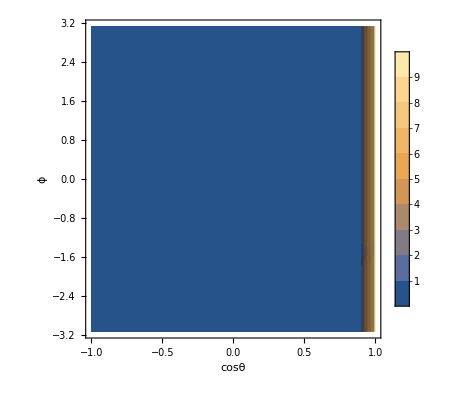

```mathematica
ListContourPlot[L2mL1Cylasfncosθϕ,PlotLegends->Automatic, FrameLabel->{"cosθ","ϕ"}]
```

```mathematica
1/(4π)(Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[1]]//Max[#]-Min[#]&)(Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[2]]//Max[#]-Min[#]&)
```

0.05

```mathematica
ListContourPlot[{ArcCos[#[[1]]]//ηfromθ,#[[2]],#[[3]]}&/@Select[L2mL1Cylasfncosθϕ,#[[3]]>0&],PlotLegends->Automatic, FrameLabel->{"η","ϕ"}]
```

-Graphics-

```mathematica
Show[
ParametricPlot3D[{
Evaluate[planeSegmentsFromCylinder[cylinderDef]]
},{r,0,cylinderDef[[5]]},{α,0,2Pi},{l,0,cylinderDef[[4]]},
PlotRange->{{-1,1},{-1,1},{-1,1}}300,BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[currentline,{s,0,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"}]
,
ListPointPlot3D[cylinderIntersectionPoints,PlotStyle->{Red,PointSize[0.02]}]
]
```

ParametricPlot3D::nonopt: Options expected (instead of {l,0,cylinderDef⟦4⟧}) beyond position 3 in ParametricPlot3D[{Evaluate[planeSegmentsFromCylinder[cylinderDef]]},{r,0,cylinderDef⟦5⟧},{α,0,2 π},{l,0,cylinderDef⟦4⟧},PlotRange→{{-1,1},{-1,1},{-1,1}} 300,BoxRatios→{1,1,1},AxesLabel→{x,y,z},Mesh→False,PlotStyle→Evaluate[(Directive[#1,Opacity[0.4]]&)/@{Red,Red,Blue,Blue,Green,Green}]]. An option must be a rule or a list of rules.

Last::nolast: {} has zero length and no last element.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot3D[{Evaluate[planeSegmentsFromCylinder[cylinderDef]]},{r,0,cylinderDef⟦5⟧},{α,0,2 π},{l,0,cylinderDef⟦4⟧},PlotRange→{{-1,1},{-1,1},{-1,1}} 300,BoxRatios→{1,1,1},AxesLabel→{x,y,z},Mesh→False,PlotStyle→Evaluate[(Directive[Slot[«1»],Opacity[«1»]]&)/@{Red,Red,Blue,Blue,Green,Green}]],,].

Show[ParametricPlot3D[{Evaluate[planeSegmentsFromCylinder[cylinderDef]]},{r,0,cylinderDef⟦5⟧},{α,0,2 π},{l,0,cylinderDef⟦4⟧},PlotRange→{{-1,1},{-1,1},{-1,1}} 300,BoxRatios→{1,1,1},AxesLabel→{x,y,z},Mesh→False,PlotStyle→Evaluate[(Directive[#1,Opacity[0.4]]&)/@{Red,Red,Blue,Blue,Green,Green}]],-Graphics3D-,-Graphics3D-]

```mathematica
ListPointPlot3D[cylinderIntersectionPoints,PlotStyle->{Red,PointSize[0.02]}]
```

-Graphics3D-

## Spherical Geometry

#### Setting up cylinder parametric definitions

```mathematica
planeSegmentsFromSphere[sphereDef_]:={
sphereDef[[1]]+sphereDef[[4]]*Cos[α],sphereDef[[2]]+sphereDef[[4]]*Sin[α]Cos[β],sphereDef[[3]]+sphereDef[[4]]*Sin[α]Cos[β]
}
```

## Tests

```mathematica
sphereDef ={0,0, 20,10} (*In the form x,y,z (of the first cap centre), and radius. All in m. x is up, y is to the right, and z is down the beampipe*)
```

{0,0,20,10}

```mathematica
{lineθ,lineϕ}={.7,0};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]}
```

{0.644218 s,0.,0.764842 s}

```mathematica
linePt1 = currentline/.s->0;
linePt2 = currentline/.s-> 1;
InfiniteLine[{linePt1,linePt2}];
coordSphere=Sphere[{sphereDef[[1]],sphereDef[[2]],sphereDef[[3]]},sphereDef[[4]]];
```

```mathematica
sphereIntsct={x,y,z}/.Solve[{x,y,z}∈HalfLine[{linePt1,linePt2}]&&{x,y,z}∈coordSphere,{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{x,y,z}

```mathematica
disTravel=EuclideanDistance[sphereIntsct[[1]],sphereIntsct[[2]]]//N
```

EuclideanDistance[x,y]

```mathematica
NumericQ[disTravel]
```

False

```mathematica
L2mL1Sphereasfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

linePt1 = currentline/.s->0;
linePt2 = currentline/.s-> 1;
coordSphere=Sphere[{sphereDef[[1]],sphereDef[[2]],sphereDef[[3]]},sphereDef[[4]]];sphereIntsct={x,y,z}/.Solve[{x,y,z}∈HalfLine[{linePt1,linePt2}]&&{x,y,z}∈coordSphere,{x,y,z}]//Quiet;

disTravel=EuclideanDistance[sphereIntsct[[1]],sphereIntsct[[2]]]//N;

sphereDis=If[NumberQ[disTravel]==True ,disTravel, 0]

}
,{cosθ,1,-1,-0.02},{ϕ,-π,π,π/10}],1]
```

{{1.,-π,20.},{1.,-(9 π)/10,20.},{1.,-(4 π)/5,20.},{1.,-(7 π)/10,20.},{1.,-(3 π)/5,20.},{1.,-π/2,20.},{1.,-(2 π)/5,20.},{1.,-(3 π)/10,20.},{1.,-π/5,20.},{1.,-π/10,20.},{1.,0,20.},{1.,π/10,20.},{1.,π/5,20.},{1.,(3 π)/10,20.},{1.,(2 π)/5,20.},{1.,π/2,20.},2089,{-1.,-π/2,0},{-1.,-(2 π)/5,0},{-1.,-(3 π)/10,0},{-1.,-π/5,0},{-1.,-π/10,0},{-1.,0,0},{-1.,π/10,0},{-1.,π/5,0},{-1.,(3 π)/10,0},{-1.,(2 π)/5,0},{-1.,π/2,0},{-1.,(3 π)/5,0},{-1.,(7 π)/10,0},{-1.,(4 π)/5,0},{-1.,(9 π)/10,0},{-1.,π,0}}
 |  |  |  |

```mathematica
Transpose[Select[L2mL1Sphereasfncosθϕ,#[[3]]>0&]][[1]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.96,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.94,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88,0.88}

```mathematica
(Transpose[Select[L2mL1Sphereasfncosθϕ,#[[3]]>0&]][[1]]//Max[#]-Min[#]&)
```

0.12

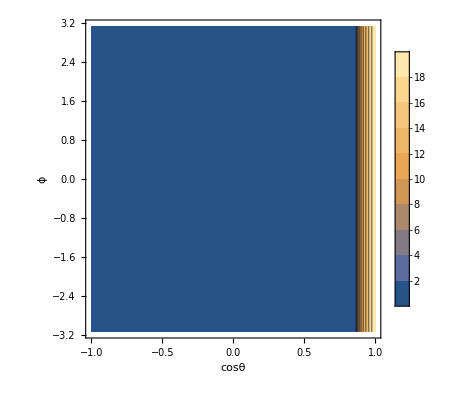

```mathematica
ListContourPlot[L2mL1Sphereasfncosθϕ,PlotLegends->Automatic, FrameLabel->{"cosθ","ϕ"}]
```

```mathematica
1/(4π)(Transpose[Select[L2mL1Sphereasfncosθϕ,#[[3]]>0&]][[1]]//Max[#]-Min[#]&)(Transpose[Select[L2mL1Sphereasfncosθϕ,#[[3]]>0&]][[2]]//Max[#]-Min[#]&)
```

0.06

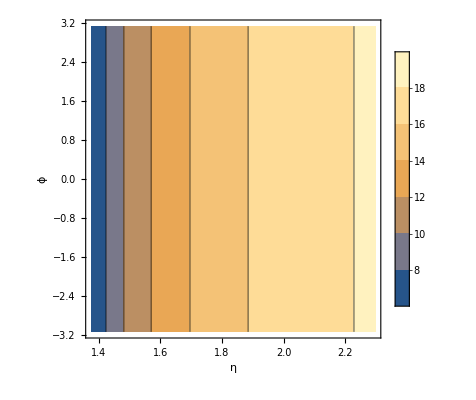

```mathematica
ListContourPlot[{ArcCos[#[[1]]]//ηfromθ,#[[2]],#[[3]]}&/@Select[L2mL1Sphereasfncosθϕ,#[[3]]>0&],PlotLegends->Automatic, FrameLabel->{"η","ϕ"}]
```

```mathematica
Show[
ParametricPlot3D[{
Evaluate[planeSegmentsFromCylinder[cylinderDef]]
},{r,0,cylinderDef[[5]]},{α,0,2Pi},{l,0,cylinderDef[[4]]},
PlotRange->{{-1,1},{-1,1},{-1,1}}300,BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[currentline,{s,0,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"}]
,
ListPointPlot3D[cylinderIntersectionPoints,PlotStyle->{Red,PointSize[0.02]}]
]
```

ParametricPlot3D::nonopt: Options expected (instead of {l,0,cylinderDef⟦4⟧}) beyond position 3 in ParametricPlot3D[{Evaluate[planeSegmentsFromCylinder[cylinderDef]]},{r,0,cylinderDef⟦5⟧},{α,0,2 π},{l,0,cylinderDef⟦4⟧},PlotRange→{{-1,1},{-1,1},{-1,1}} 300,BoxRatios→{1,1,1},AxesLabel→{x,y,z},Mesh→False,PlotStyle→Evaluate[(Directive[#1,Opacity[0.4]]&)/@{Red,Red,Blue,Blue,Green,Green}]]. An option must be a rule or a list of rules.

Last::nolast: {} has zero length and no last element.

Show::gcomb: Could not combine the graphics objects in Show[ParametricPlot3D[{Evaluate[planeSegmentsFromCylinder[cylinderDef]]},{r,0,cylinderDef⟦5⟧},{α,0,2 π},{l,0,cylinderDef⟦4⟧},PlotRange→{{-1,1},{-1,1},{-1,1}} 300,BoxRatios→{1,1,1},AxesLabel→{x,y,z},Mesh→False,PlotStyle→Evaluate[(Directive[Slot[«1»],Opacity[«1»]]&)/@{Red,Red,Blue,Blue,Green,Green}]],,].

Show[ParametricPlot3D[{Evaluate[planeSegmentsFromCylinder[cylinderDef]]},{r,0,cylinderDef⟦5⟧},{α,0,2 π},{l,0,cylinderDef⟦4⟧},PlotRange→{{-1,1},{-1,1},{-1,1}} 300,BoxRatios→{1,1,1},AxesLabel→{x,y,z},Mesh→False,PlotStyle→Evaluate[(Directive[#1,Opacity[0.4]]&)/@{Red,Red,Blue,Blue,Green,Green}]],-Graphics3D-,-Graphics3D-]

```mathematica
ListPointPlot3D[cylinderIntersectionPoints,PlotStyle->{Red,PointSize[0.02]}]
```

-Graphics3D-